```mathematica
g=Interpolation[{{2.0,39.1},
{2.3,39.2},
{2.6,40.8},
{2.8,41.6},
{2.9,41.2},
{3.0,43.7},
{3.3,45.9},
{3.6,47.4},
{3.8,47.3},
{3.9,48.8},
{4.0,52.3},
{4.3,52.3},
{4.6,52.3},
{4.8,48.7},
{4.9,47.3},
{5.0,46.2},
{5.3,35.7},
{5.6,34.4},
{5.8,30.6},
{5.9,29.6},
{6.0,26.2}}]
```

InterpolatingFunction[{{2.,6.}},<>]

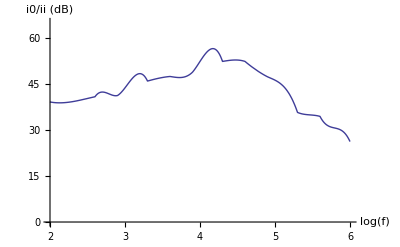

```mathematica
Plot[g[x],{x,2,6}, PlotRange->{{2,6},{0,65}},AxesLabel->{"log(f)","i0/ii (dB)"}]
```

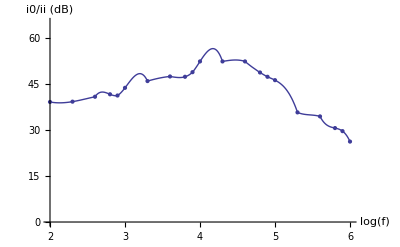

```mathematica
Show[%,ListPlot[{{2.0,39.1},{2.3,39.2},{2.6,40.8},{2.8,41.6},{2.9,41.2},{3.0,43.7},{3.3,45.9},{3.6,47.4},{3.8,47.3},{3.9,48.8},{4.0,52.3},{4.3,52.3},{4.6,52.3},{4.8,48.7},{4.9,47.3},{5.0,46.2},{5.3,35.7},{5.6,34.4},{5.8,30.6},{5.9,29.6},{6.0,26.2}}]]
```

```mathematica
FindMaximum[g[x],{x,4}]
```

{56.472,{x→4.1718}}

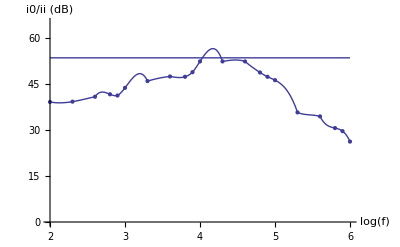

```mathematica
Show[Plot[g[x],{x,2,6}, PlotRange->{{2,6},{0,65}},AxesLabel->{"log(f)","i0/ii (dB)"}],ListPlot[{{2.0,39.1},{2.3,39.2},{2.6,40.8},{2.8,41.6},{2.9,41.2},{3.0,43.7},{3.3,45.9},{3.6,47.4},{3.8,47.3},{3.9,48.8},{4.0,52.3},{4.3,52.3},{4.6,52.3},{4.8,48.7},{4.9,47.3},{5.0,46.2},{5.3,35.7},{5.6,34.4},{5.8,30.6},{5.9,29.6},{6.0,26.2}}],Plot[53.472,{x,2,6}, PlotRange->{{2,6},{0,65}},AxesLabel->{"log(f)","i0/ii (dB)"}]]
```

```mathematica
FindMaximum[g[x],{x,4}]
```

{56.472,{x→4.1718}}

```mathematica
FindRoot[g[x]==53.472,{x,4.1}]
```

{x→4.03192}

```mathematica
g[4.0319180917401445]
```

53.472

```mathematica
FindRoot[g[x]==53.472,{x,4.18}]
```

{x→4.28199}

```mathematica
g[4.281987917407768]
```

53.472